# An Introduction to Mathematica

Author: Nicholas Loutrel
Date last modified: 29/11/2023

## Introduction & Basic Operations

### Notebook Basics

Mathematica notebooks work in a near identical way to Jupyter/IPython notebooks. The notebooks contains cells, with each cell containing specific codes and commands, which are run by pressing ‘SHIFT + ENTER’.

```mathematica
2+2
```

4

‘In[#]’ are input cells, while ‘Out[#]’ are the output from the corresponding input cell.

Pressing ‘ENTER’ adds a new line within the input cell. Multiple expression can be evaluated per input cell using this method:

```mathematica
2+2
3+1
```

4

4

### Basic Arithmetic Operations

All basic math operations are specified with their corresponding symbols: + (addition), - (subtraction), * (multiplication), / (division), ^(exponentiation). Note the difference between Python and Mathematica for exponentiation!

```mathematica
8+13
```

21

```mathematica
21-8
```

13

```mathematica
2*2
```

4

```mathematica
4/2
```

2

```mathematica
2^2
```

4

Multiplication can also be achieved by adding in parentheses and/or spaces.

```mathematica
2 2
```

4

```mathematica
2(2)
```

4

But, remember order of operations!

```mathematica
2(1+1)
```

```mathematica
2 1+1
```

Mathematica contains a number of special symbols, which can be created by entering ‘Esc + Symbol/Key + Esc’. For example, the infinity symbol is obtained by entering ‘Esc  Inf  Esc’:

```mathematica
∞
```

The multiplication symbol can take a special form using this method (input ‘Esc *  Esc’):

```mathematica
2×2
```

Other special formatting can be obtained through the ‘Ctrl + Key’ command. For example, division (‘Ctrl + /’) and exponentiation (‘Ctrl + ^’):

```mathematica
2/3
```

```mathematica
2^3
```

### Variables

Any letter entered as input is automatically treated as a variable. No need to tell Mathematica explicitly!

```mathematica
x
```

x

Notice the color of ‘x’ in the input cell (it’s blue, important in a moment).

Not all letters can be used as variables, as some are used for built-in functions or special mathematical symbols. For example, capital D is the function for differentiation (more on this later).

```mathematica
D[x,x]
```

1

Values can be assigned to variables using the ‘=’ symbol. Output for an input cell can be suppressed using the ‘;’ at the end of the cell.

```mathematica
x=2;
```

Now, notice again the color of ‘x’ from the input (both here and previously). It’s now black, which indicates visibly that it is already assigned a value. This also works if the letter is used internally for a function.

```mathematica
D
```

D

Variable names do not need to be single letters. They can be words ...

```mathematica
myVariable
```

myVariable

... or even Greek letters (input using ‘Esc + name_of_letter + Esc’).

```mathematica
α
```

α

But they cannot have any special character such as underscore (_), exclamation (!), etc. They also can’t start with numbers.

```mathematica
2myVariable
```

2 myVariable

Mathematica just treats this as standard multiplication.

As a final note, be careful when assigning values to variables not use the double equals sign ‘==’. This is used for boolean statements:

```mathematica
x==2
```

```mathematica
x/2
```

1

If you inadvertently assign a variable a value, you can overwrite it by reassigning it’s value (if you intend for it to have one) ...

```mathematica
x=3;
x==3
```

... or you can use the ‘Clear’ function.

```mathematica
Clear[x]
```

Notice again that ‘x’ changed color to indicate it is unassigned any value.

### Substitution

Suppose you have the following expression ...

```mathematica
x^2+2x+1
```

```mathematica
9
Clear[x]
```

9

... and you want to know what it’s value is without globally assigning a variable to ‘x.’ You can do this with substitutions, which are performed with the ‘/.{rule_to_sub}’ :

```mathematica
x^2+2x+1/.{x->5}
```

36

Notice again that ‘x’ is still unassigned. Substitutions generally apply their rules to the entirety of the cell, but do respect order of operations rules:

```mathematica
x^2+(2x+1)/.{x->2}
x^2+(2x+1/.{x->2})
```

Be careful when applying operations after the substitution on the input cell. Mathematica will complain:

```mathematica
x^2+(2x+1)/.{x->2}*2
```

Use parentheses if you need to do this:

```mathematica
(x^2+(2x+1)/.{x->2})*2
```

### Functions

All functions in Mathematica take inputs through [], not parentheses, which are only used for specifying parts of expressions. Functions you create follow the same naming rules as variables. To specify inputs, use the underscore, while to specify the functions itself, use ‘:=’:

```mathematica
f[x_]:=x^2+2x+1
```

Notice again the color of the variable ‘x’, which is green in this case. This tells you that it is an internal/input variable to the function ‘f’. Also, ‘f’ is now assigned to be a function which takes ‘x’ as an input. It is possible to override the functions current assignment with ‘=’, so be careful!

```mathematica
f=2;
f==2
```

True

```mathematica
Clear[f]
f[x_]:=x^2+2x+1
```

To evaluate a function, simply add an input:

```mathematica
f[2]
f[y]
```

9

1+2 y+y^2

Note that functions respect the values of global variables:

```mathematica
a=2;
f[x_]:=x^2+a x+1
```

```mathematica
f[2]
f[y]
```

9

1+2 y+y^2

To specify more than one variable, use a comma for multiple inputs:

```mathematica
g[x_,y_,z_]:=x^2+y^2+z^2
```

Functions can also be evaluated using the @ symbol and //. In these cases, the function should be understood as acting upon something. Note that // also applies to the entire input line like substitutions:

```mathematica
f@2
```

9

```mathematica
2//f
```

9

```mathematica
1+1//f
```

9

Some built-in functions:

```mathematica
Cos[0]
Sin[0]
Sqrt[2]
Exp[-10]
Log[ⅇ]
Log10[10]
```

1

0

√2

1/ⅇ^10

1

1

### Numerical Evaluation & Precision

Consider the fraction:

```mathematica
2/3
```

2/3

Mathematic doesn’t give a decimal answer for it. This is because Mathematica can treat numbers with arbitrary floating point precision. To evaluate the fraction (or any number for that matter) to a decimal, use the ‘N’ function.

```mathematica
N[2/3]
N@(2/3)
2/3//N
```

0.666667

0.666667

0.666667

Note that the output only has a finite number of decimal points. You can change this by specify an additional option of ‘N’:

```mathematica
N[2/3,15]
```

0.666666666666667

```mathematica
N[2/3,100]
```

0.6666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667

Be careful though: if you give Mathematica decimals on number as an input, it will automatically evaluate the expression but only have finite precision.

```mathematica
2./3
```

0.666667

```mathematica
N[2./3.,15]
```

0.666667

```mathematica
NumberForm[0.6666666666666666,16]
```

0.6666666666666666

### Help

To get help/documentation about built in Mathematica functions, use ‘?’:

```mathematica
?N
```

## Simplification

### Simplify & FullSimplify

The simplest built-in function for simplification is ‘Simplify’:

```mathematica
Simplify[x^2-2x+1]
```

(-1+x)^2

Another example, using trig functions and the ‘%’ symbol. ‘%’ tells Mathematica to take the output of the previous input and do something to it:

```mathematica
Sin[x]^2+Cos[x]^2
Simplify[%]
```

Cos[x]^2+Sin[x]^2

1

‘Simplify’ uses a variety of algebraic transformations to try to simplify an expression. But there are examples where it doesn’t simplify expressions in the desired way:

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%]
```

√(x^2)

√(x^2)

The above example highlights a critical behavior of Mathematica, it assumes all variables are complex! To fix this, apply assumptions:

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x>0}]
%/.{x->2}
```

√(x^2)

x

2

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x<0}]
%/.{x->-2}
```

√(x^2)

-x

2

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x∈ Reals}]
%/.{x->2}
%%/.{x->-2}
```

√(x^2)

Abs[x]

2

2

Note that the final expression varies depending on the assumptions, but they all give us the correct answer (Mathematica always assumes the square root is positive definite), with the final example being the most general. Note that substitution rules do not respect assumptions applied in previous simplifications steps:

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x<0}]
%/.{x->2}
```

√(x^2)

-x

-2

Another example using logarithms:

```mathematica
Simplify[Log[x]+Log[y]]
Simplify[Log[x]+Log[y],Assumptions->{x>0&&y>0}]
```

Log[x]+Log[y]

Log[x y]

When simplifying expressions with special functions, ‘Simplify’ may not be enough. Take for example, the Gamma function Γ(x), which for integer values reduces to the factorial Γ(n)=(n-1)!,  but generalizes to non-integer values. From the rules of factorials n Γ(n) = n!, and the generalization to arbitrary real numbers is x Γ(x) = Γ(x+1). But, ‘Simplify’ can’t do this:

```mathematica
Gamma[3]
(3-1)!
```

2

2

```mathematica
3*Gamma[3]
3!
```

6

6

```mathematica
2.1*Gamma[2.1]
Gamma[2.1+1]
```

2.19762

2.19762

```mathematica
Simplify[x Gamma[x]]
```

x Gamma[x]

In such cases, ‘FullSimplify’ may be used:

```mathematica
FullSimplify[x Gamma[x]]
```

Gamma[1+x]

‘FullSimplify’ applies a larger set of transformation rules than ‘Simplify’, but it is slower as a result, especially when dealing with very complicated expression. Two more examples highlighting the difference between ‘Simplify’ and ‘FullSimplify’:

1) Hyperbolic functions:

```mathematica
Simplify[Cosh[x]-Sinh[x]]
FullSimplify[Cosh[x]-Sinh[x]]
```

Cosh[x]-Sinh[x]

ⅇ^-x

2) √2+√3-√(5+2 √6)=0

```mathematica
Simplify[Sqrt[2]+Sqrt[3]-Sqrt[5+2Sqrt[6]]]
FullSimplify[Sqrt[2]+Sqrt[3]-Sqrt[5+2Sqrt[6]]]
```

√2+√3-√(5+2 √6)

0

‘FullSimplify’ may still need assumptions though:

```mathematica
FullSimplify[Sqrt[x^2]]
FullSimplify[Sqrt[x^2],Assumptions->{x>0}]
```

√(x^2)

x

### Expand & ExpandAll

Expressions involving polynomials can be expanded out using the ‘Expand’ function:

```mathematica
Expand[(x+1)^2(x-1)^2]
Expand[x(x^2+1)(x^3+3)]
```

1-2 x^2+x^4

3 x+3 x^3+x^4+x^6

‘Expand’ doesn’t operate within “subexpressions.” For example:

```mathematica
Expand[Sqrt[(1+x)^2]]
```

√((1+x)^2)

To expand the polynomial inside of the square root, use ‘ExpandAll’:

```mathematica
ExpandAll[Sqrt[(1+x)^2]]
```

√(1+2 x+x^2)

Similarly, ‘Expand’ only expands the numerator of expressions:

```mathematica
Expand[(x y+x^2+2 z^4)/(y+z)^4]
```

x^2/(y+z)^4+(x y)/(y+z)^4+(2 z^4)/(y+z)^4

Use ‘ExpandAll’ to expand both numerator and denominator:

```mathematica
ExpandAll[(x y+x^2+2 z^4)/(y+z)^4]
```

x^2/(y^4+4 y^3 z+6 y^2 z^2+4 y z^3+z^4)+(x y)/(y^4+4 y^3 z+6 y^2 z^2+4 y z^3+z^4)+(2 z^4)/(y^4+4 y^3 z+6 y^2 z^2+4 y z^3+z^4)

### PowerExpand & ComplexExpand

To expand powers in expressions, use ‘PowerExpand’:

```mathematica
PowerExpand[Sqrt[(1+x)^2]]
PowerExpand[x^2]
PowerExpand[Sqrt[x^2]]
PowerExpand[Sqrt[x y]]
PowerExpand[(-x)^(1/3)]
```

1+x

x^2

x

√x √y

(-1)^(1/3) x^(1/3)

Notice that with ‘PowerExpand’, we don’t need assumptions like we did with ‘Simplify’:

```mathematica
Simplify[Sqrt[x^2],Assumptions->{x>0}]
PowerExpand@Sqrt[x^2]
```

x

x

We can also expand assuming that all variables/expressions are complex using ‘ComplexExpand’:

```mathematica
ComplexExpand[(-1)^(1/3)]
```

1/2+(ⅈ √3)/2

Note that to input the imaginary unit, you can either type capital ‘I’ or ‘Esc + ii + Esc’:

```mathematica
I
```

ⅈ

```mathematica
ⅈ
```

ⅈ

```mathematica
ComplexExpand[Sin[x+I y]]
ComplexExpand[Sin[x+ⅈ y]]
```

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

```mathematica
Factoring Polynomials
```

Polynomials can be factored using the ‘Factor’ function:

```mathematica
Factor[x^2-y^2]
Factor[x^2-2x+1]
Factor[x^10-1]
```

(x-y) (x+y)

(-1+x)^2

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

Not all trig expressions can be simplified/manipulated with ‘Simplify’ and ‘Expand’.

```mathematica
Simplify[Sin[x]Cos[x]]
Simplify[Sin[x]^2]
Expand[Cos[3x]]
```

Cos[x] Sin[x]

Sin[x]^2

Cos[3 x]

For these, use ‘TrigReduce’ and ‘TrigExpand’:

```mathematica
TrigReduce[Sin[x]Cos[x]]
TrigReduce[Sin[x]^2]
TrigExpand[Cos[3x]]
```

1/2 Sin[2 x]

1/2 (1-Cos[2 x])

Cos[x]^3-3 Cos[x] Sin[x]^2

Generically, ‘TrigExpand’ takes functions of the form cos(n*x) or sin(n*x), and transforms them to forms contain [cos(x)]^n and [sin(x)]^n. ‘TrigReduce’ does the reverse of this.

```mathematica
TrigExpand[Sin[4x]]
TrigReduce[%]
```

4 Cos[x]^3 Sin[x]-4 Cos[x] Sin[x]^3

Sin[4 x]

Trig functions can also be converted to complex exponentials and vice versa, using ‘TrigToExp’ and ‘ExpToTrig’.

```mathematica
TrigToExp[Cos[3x]]
ExpToTrig[Exp[ⅈ x]]
```

1/2 ⅇ^(-3 ⅈ x)+1/2 ⅇ^(3 ⅈ x)

Cos[x]+ⅈ Sin[x]

## Solving Systems of Algebraic Equations

### Solving Algebraic Equations

The general function to solve algebraic equations is “Solve”. The output is always a list of substitution rules, ensuring that variables you use do not get overwritten. If more than one solution is found, you can take only one using [[n]] brackets.

```mathematica
Clear[a]
Solve[a x^2+b x+c==0,x]
x/.%[[1]]
x/.Flatten@%%
x/.%%%
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

(-b-√(b^2-4 a c))/(2 a)

(-b-√(b^2-4 a c))/(2 a)

{(-b-√(b^2-4 a c))/(2 a),(-b+√(b^2-4 a c))/(2 a)}

“Solve” also works with numerical coefficients, and can find complex solutions.

```mathematica
Solve[4 x^2+2x+1==0,x]
Solve[x^5==1,x]
%//ComplexExpand
```

{{x→1/4 (-1-ⅈ √3)},{x→1/4 (-1+ⅈ √3)}}

{{x→1},{x→-(-1)^(1/5)},{x→(-1)^(2/5)},{x→-(-1)^(3/5)},{x→(-1)^(4/5)}}

{{x→1},{x→-1/4-(√5)/4-ⅈ √(5/8-(√5)/8)},{x→-1/4+(√5)/4+ⅈ √(5/8+(√5)/8)},{x→-1/4+(√5)/4-ⅈ √(5/8+(√5)/8)},{x→-1/4-(√5)/4+ⅈ √(5/8-(√5)/8)}}

“Solve” can also take inequalities and systems of equations.

```mathematica
Solve[4 x^2+2x-1==0 &&x>0,x]
Solve[{4 x^2+2x-1==0,x>0},x]
```

{{x→1/4 (-1+√5)}}

{{x→1/4 (-1+√5)}}

You can even specify the domain of any solutions.

```mathematica
Solve[x^5==1,x,Reals]
Solve[x^5==1,x,Integers]
Solve[x^5==1,x,Complexes]
```

{{x→1}}

{{x→1}}

{{x→1},{x→-(-1)^(1/5)},{x→(-1)^(2/5)},{x→-(-1)^(3/5)},{x→(-1)^(4/5)}}

But “Solve” is not all powerful! It primarily deals with linear and polynomial equations.

```mathematica
Solve[1/10==x-Sin[x],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[1/10==x-Sin[x],x]

“Solve” (and Mathematica in general), can also be horribly obtuse!

```mathematica
Solve[P^2==a^3,a,Reals]
```

{{a→Root[-P^2+#1^3&,1]}}

```mathematica
Solve[P^2==a^3,a]
```

{{a→P^(2/3)},{a→-(-1)^(1/3) P^(2/3)},{a→(-1)^(2/3) P^(2/3)}}

There is also a numerical version of “Solve” called “NSolve”, for cases where you are only looking for approximate answers. “NSolve” has the same limitations as “Solve”.

```mathematica
Solve[x^10-8 x^7+3 x^4-1==0,x]
NSolve[x^10-8 x^7+3 x^4-1==0,x]
```

{{x→Root-0.657Root[-1+3 #1^4-8 #1^7+#1^10&,1]-0.6574096598826199},{x→Root1.97Root[-1+3 #1^4-8 #1^7+#1^10&,2]1.9673702166950269},{x→Root-0.982-1.70 ⅈRoot[-1+3 #1^4-8 #1^7+#1^10&,3]-0.9824864183287173},{x→Root-0.982+1.70 ⅈRoot[-1+3 #1^4-8 #1^7+#1^10&,4]-0.9824864183287173},{x→Root-0.494-0.697 ⅈRoot[-1+3 #1^4-8 #1^7+#1^10&,5]-0.49425081204297544},{x→Root-0.494+0.697 ⅈRoot[-1+3 #1^4-8 #1^7+#1^10&,6]-0.49425081204297544},{x→Root0.0930-0.676 ⅈRoot[-1+3 #1^4-8 #1^7+#1^10&,7]0.09300512534993984},{x→Root0.0930+0.676 ⅈRoot[-1+3 #1^4-8 #1^7+#1^10&,8]0.09300512534993984},{x→Root0.729-0.240 ⅈRoot[-1+3 #1^4-8 #1^7+#1^10&,9]0.7287518266155495},{x→Root0.729+0.240 ⅈRoot[-1+3 #1^4-8 #1^7+#1^10&,10]0.7287518266155495}}

{{x→-0.982486-1.70311 ⅈ},{x→-0.982486+1.70311 ⅈ},{x→-0.65741},{x→-0.494251-0.696934 ⅈ},{x→-0.494251+0.696934 ⅈ},{x→0.0930051-0.675781 ⅈ},{x→0.0930051+0.675781 ⅈ},{x→0.728752-0.240197 ⅈ},{x→0.728752+0.240197 ⅈ},{x→1.96737}}

```mathematica
NSolve[0.1==x-Sin[x],x]
```

NSolve[0.1==x-Sin[x],x]

### FindRoot: A more powerful solver

“Solve” and “NSolve” are limited to special classes of algebraic equations where exact or approximate techniques works. But there are far more powerful numerical algorithms (Newton’s method, secant method, etc.) to solve equations. These are implemented in Mathematica using the “FindRoot” function. The downside to these methods is you have to feed “FindRoot” an estimate of where the answer is (this is a result of the numerical methods it uses).

```mathematica
FindRoot[x^2-1==0,{x,1.1}]
```

{x→1.}

A detour on plotting (for finding a good guess):

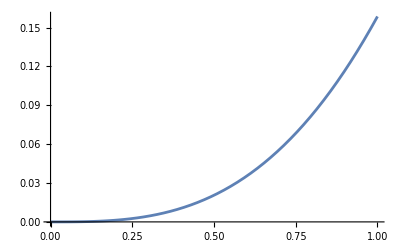

```mathematica
Plot[x-Sin[x],{x,0,1}]
```

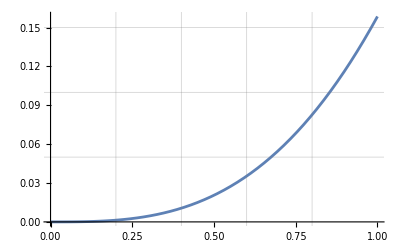

```mathematica
Plot[x-Sin[x],{x,0,1},GridLines->{{0.2,0.4,0.6,0.8},{0.05,0.1,0.15}}]
```

```mathematica
FindRoot[0.1==x-Sin[x],{x,0.8}]
(x-Sin[x]/.%)
%-0.1
```

{x→0.85375}

0.1

-2.77556×10^-17

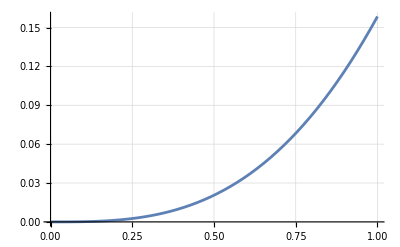

```mathematica
Plot[x-Sin[x],{x,0,1},GridLines-> Automatic]
```

## Calculus

### Differentiation

As mentioned at the beginning of this notebook, “D” corresponds to the built-in derivative functions within Mathematica.

```mathematica
D[x^2,x]
```

2 x

The function takes inputs in the form D[func_, vars_], the first of which is the function to differentiate and the second is the variable to differentiate with respect to. So this allows a very easy extension to multiple variables:

```mathematica
D[x y,y]
```

x

What if you want to take the second derivative? You might be tempted to do:

```mathematica
D[D[x^2,x],x]
```

2

BUT, you don’t need to do this! The following also works:

```mathematica
D[x^2,x,x]
D[x^2,{x,2}]
D[x y,x,y]
```

2

2

1

“D” can also be used to compute things like the gradient (vector) or Hessian/Jacobian (matrix):

```mathematica
D[x y,{{x,y}}] (*Gradient*)
D[x y,{{x,y},2}] (*Hessian/Jacobian*)
MatrixForm@%
```

{y,x}

{{0,1},{1,0}}

(0 | 1
1 | 0)

A few more examples:

```mathematica
Clear[f]
Clear[g]
D[x^n,x]
D[f[x]^n,x]
D[f[x]g[x],x]
D[f[x]/g[x],x]
D[a f[x]+b g[x],x]
```

n x^(-1+n)

n f[x]^(-1+n) f'[x]

g[x] f'[x]+f[x] g'[x]

f'[x]/g[x]-(f[x] g'[x])/g[x]^2

a f'[x]+b g'[x]

Like many other things, there is a special symbol for the derivative operator that can be achieved using ‘Esc + pd + Esc’. To specify the variable to differentiate with respect to, use ‘Ctrl + Underscore’:

```mathematica
D[f[x], x]
```

f'[x]

### Integration

The function for performing analytic integration in Mathematica is “Integrate”:

```mathematica
Integrate[x^2,x]
```

```mathematica
x^3/3
Integrate[1/(x^2+1)^2,x]
```

x^3/3

1/2 (x/(1+x^2)+ArcTan[x])

The above input/output shows an example of indefinite integration. “Integrate” has similar input structure to “D”:
D[func_, {vars_, n}]
Integrate[func_, {vars_, a, b}]
There are two differences though. The first is when specifying repeated integration. The following doesn’t work

```mathematica
Integrate[x^2,{x,2}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {x,2}.

Integrate[x^2,{x,2}]

... but the following does!

```mathematica
Integrate[x^2,x,x]
```

x^4/12

The reason is due to the second difference, which is that integrals can also be definite, and you can specify the limits of integration in the following way:

```mathematica
Integrate[x^2,{x,0,1}]
Integrate[Exp[x],{x,y,1}]
```

1/3

ⅇ-ⅇ^y

You can also perform integration with respect to multiple variables with a single command. For example, here is an example of the orthogonality of spherical harmonics:

```mathematica
Integrate[SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
Integrate[SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[2,-1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

1

0

“Integrate” is powerful and knows the results of many integral tables, for example
(∫_1)^∞dn n^-2 K_(2/3)(n z)K_(1/3)(n z)

```mathematica
Integrate[n^-2 BesselK[2/3,n z] BesselK[1/3,n z],{n,1,∞},Assumptions->{z>0&&z<1}]
```

1/(640 √3 z)π (-(1440 √π z^(2/3) HypergeometricPFQ[{-2/3,5/6},{1/3,2/3,4/3},z^2])/Gamma[1/6]+(4320 √π z^(4/3) HypergeometricPFQ[{-1/3,7/6},{2/3,4/3,5/3},z^2])/Gamma[-1/6]-243 z^4 HypergeometricPFQ[{1,1,5/2},{2,7/3,8/3,3},z^2]-40 (-8+9 z^2 (-7+4 EulerGamma+Log[729/16])+36 z^2 Log[z]))

### Series Expansions

Suppose you have a function and want to study it’s local behavior around a point (i.e. you need to compute it’s Taylor expansion/series). Mathematica has a function for this called “Series”:

```mathematica
Series[Sin[x],{x,0,5}]
```

x-x^3/6+x^5/120+O[x]^6

The first input is always the function you desire to series expand, while the second is an array {} with structure {var, pt, order}. ‘var’ is the variable to series expand in, ‘pt’ is the value of the variable to expands around, and ‘order’ is the order of the expansion (highest power of ‘var’ in the series).

```mathematica
Clear[f]
Series[f[x],{x,x0,3}]
```

f[x0]+f'[x0] (x-x0)+1/2 f''[x0] (x-x0)^2+1/6 f^(3)[x0] (x-x0)^3+O[x-x0]^4

The output always has the O[x^n] symbol at the end of it, which indicates the remainder of the series expansion. From a formal theory perspective, this is fine, but you may notice Mathematica will not want to simplify/manipulate an expressions with this symbol. To get rid of it, apply the “Normal” function.

```mathematica
Normal@Series[f[x],{x,x0,2}]
Normal[Series[f[x],{x,x0,2}]]
Series[f[x],{x,x0,2}]//Normal
```

f[x0]+(x-x0) f'[x0]+1/2 (x-x0)^2 f''[x0]

f[x0]+(x-x0) f'[x0]+1/2 (x-x0)^2 f''[x0]

f[x0]+(x-x0) f'[x0]+1/2 (x-x0)^2 f''[x0]

“Series” can be useful for taking limits:

```mathematica
Sin[x]/x/.{x->0}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
Sinc[x]/.{x->0}
```

1

```mathematica
Series[Sin[x]/x,{x,0,3}]
Normal@%
%/.{x->0}
```

1-x^2/6+O[x]^4

1-x^2/6

1

Note, that “Series” can also compute asymptotic series:

```mathematica
Series[1/Sqrt[1+x^2],{x,∞,3}]
```

1/x-1/(2 x^3)+O[1/x]^4

### Numerical Integration

We covered “Integrate” already, but sometimes you may encounter complicated integrals that don’t have analytic solutions.

```mathematica
Integrate[1/x Cos[Log[x]/x],{x,0,1}]
```

∫_0^1 Cos[Log[x]/x]/x ⅆx

For these, you can use numerical integration via “NIntegrate”:

```mathematica
NIntegrate[1/x Cos[Log[x]/x],{x,0,1}]
```

0.323367

“NIntegrate” has much of the same functionality of “Integrate”, it just gives you numerical answers instead of analytic ones (so you can’t use it for indefinite integrals, sorry). Here’s a really pedantic integral that has an exact answer we can compare to the numerical one:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2}]
exact=Integrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2}]
%%-%//N
```

3.52549

1/2 Log[577+408 √2]

-4.36428×10^-8

Pretty accurate, but we can do better by specify accuracy and precision tolerances. These are specified with the “AccuracyGoal” and “PrecisionGoal”, which have the following syntax:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2},AccuracyGoal->13,PrecisionGoal->13]
exact-%//N
```

3.52549

-1.9984×10^-14

After each ‘->’ is a number which corresponds to desired accuracy/precision tolerance of order 10^-number. This can obviously be seen from the error computed above. The default for both of these is half “WorkingPrecision” (double precision for most applications), so the default is 7.

By default, Mathematica attempts to select the best numerical method to perform the integral out of all possible methods implemented (called the “Automatic” method). But, we can explicitly specify this with the “Method” option. For example, here’s the same integral above, but now using Monte Carlo integration:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2},Method->"MonteCarlo",AccuracyGoal->13,PrecisionGoal->13]
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 3.47604 and 0.0178149 for the integral and error estimates.

3.47604

Mathematica complains because the default options of its Monte Carlo routine are not sufficient to obtain the desired accuracy and precision tolerances. We can fix this by specifying options within the Monte Carlo method:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2},Method->{"MonteCarlo",MaxPoints->10^6},AccuracyGoal->13,PrecisionGoal->13]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 3.53235 and 0.00645506 for the integral and error estimates.

3.53235

Obviously, this helps beat down the error in the Monte Carlo estimate, but is still not enough to reach the accuracy/precision tolerances. This is a result of the chosen method not being an optimal choice. Generally, when performing numerical integration (or numerically solving differential equations like we’ll see later), it’s best to let Mathematica choose the method for you, unless of course you know what you are doing.

The Monte Carlo method is also quite a bit slower than the method selected automatically by Mathematica. As a general rule, Mathematica is the slowest program you can pick for doing anything numerical. It’s much better to use numerical methods in something like Python, or even better, C and/or Fortran. Mathematica’s numerical routines are just as powerful as those in other languages, it’s just painfully slow most of the time. The upside is that you can seamlessly transition from analytic calculations to numerical ones within Mathematica. No need to explicitly recode things! (Assuming you can deal with the slow speed).

## Differential Equations

### DSolve

Suppose you have the following differential equations: (∂_x)^2 y(x) + w^2 y(x) = 0. You can obtain the solution using the “DSolve” function:

```mathematica
DSolve[{y''[x]+w^2 y[x]==0},y[x],x]
```

{{y[x]→C[1] Cos[w x]+C[2] Sin[w x]}}

The output for “DSolve” is always in the form of a substitution rule. “DSolve” will also always give you the most general solution, with constants of integration unspecified. These can be fixed by specifying initial/boundary conditions:

```mathematica
DSolve[{y''[x]+w^2 y[x]==0,y[0]==1,y'[0]==0},y[x],x]
```

{{y[x]→Cos[w x]}}

The syntax for “DSolve”: DSolve[{eqn1, eqn2, ..., cond1, cond2, ...}, {funcs}, {vars}]

A few more examples:

```mathematica
(*1st Order ODE*)
DSolve[{y'[x]-y[x]==0,y[2]==1},y[x],x]
```

{{y[x]→ⅇ^(-2+x)}}

```mathematica
(*Bessel's equation*)
DSolve[{y''[x]+1/x y'[x]+(x^2-n^2)/x^2 y[x]==0},y[x],x]
```

{{y[x]→BesselJ[n,x] C[1]+BesselY[n,x] C[2]}}

```mathematica
(*2D wave equation*)
DSolve[{-1/c^2 D[z[t,x],{t,2}]+D[z[t,x],{x,2}]==0},z[t,x],{t,x},Assumptions->{c>0}]
```

{{z[t,x]→C[1][-c t+x]+C[2][c t+x]}}

```mathematica
(*Sturm-Liouville problem*)
DSolve[{y''[x]+w^2 y[x]==0,y[0]==0,y[π]==0},y[x],x]
```

{{y[x]→Piecewise[{{C[1] Sin[√(w^2) x], n∈ℤ&&n≥1&&w^2==n^2}, {0, True}}]}}

```mathematica
(*Coupled DEs*)
DSolve[{y'[t]+x[t] y[t]==0,x'[t]-y[t]x[t]==0},{x[t],y[t]},t]
```

{{y[t]→C[1]-(ⅇ^(t C[1]) C[1])/(ⅇ^(t C[1])-ⅇ^(C[1] C[2])),x[t]→(ⅇ^(t C[1]) C[1])/(ⅇ^(t C[1])-ⅇ^(C[1] C[2]))}}

### NDSolve

```mathematica
Clear[a]
```

Consider the Duffing oscillator: (∂_t)^2 y+2a ∂_t y+y+ϵ y^3=cos(w t). This is a common non-linear oscillator equation and does not have an exact (closed-form), analytic solution:

```mathematica
DSolve[{y''[t]+2a y'[t]+y[t]+ϵ y[t]^3==Cos[w t]},y[t],t]
```

DSolve[{y[t]+ϵ y[t]^3+2 a y'[t]+y''[t]==Cos[t w]},y[t],t]

But, it can be solved numerically. The numerical differential equation solver in Mathematica is called “NDSolve”. It has similar syntax to “DSolve”, with a few exceptions. First, you always have to specify initial/boundary conditions for the problem you want to solve numerically. Second, you have to give it a domain to integrate over instead of just the dependent variable. This is specified by {var, min, max} after the function you want to solve for in the syntax. Also, much like “NIntegrate”, you should specify accuracy and precision goals, and any other options you care for (if you know what you’re doing).

```mathematica
sol=NDSolve[{y''[t]-0.025y'[t]+y[t]+0.1 y[t]^3==Cos[2.1t],y[0]==1,y'[0]==0},y,{t,0,60},Method->"ImplicitRungeKutta",AccuracyGoal->13,PrecisionGoal->13,MaxSteps->Infinity]
```

{{y→InterpolatingFunction[…]}}

Notice that the solution is given as an interpolating function, instead of a set of data points like you might find from numerical methods in Python/C/C++/etc. Mathematica automatically interpolates the data it gets from running “NDSolve”. The data is stored so you can get it from the functions.

```mathematica
ynum=(y/.Flatten@sol)[t];
```

```mathematica
ynum[[0]]
PropertyList[%]
```

InterpolatingFunction[…]

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid,VectorEvaluate}

```mathematica
ynum[[0]]["ValuesOnGrid"]
Flatten@ynum[[0]]["Coordinates"]
ydat=Transpose[{%,%%}]
```

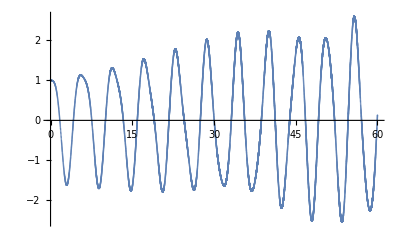

```mathematica
ListPlot[ydat]
```

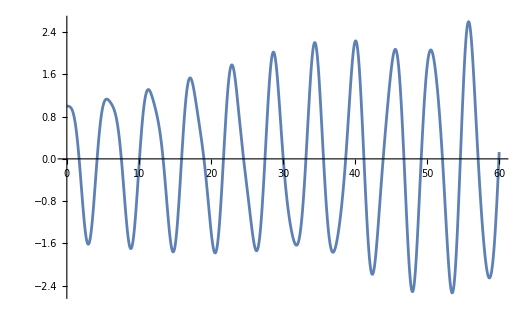

```mathematica
Plot[ynum,{t,0,60}]
```

Here is another (simpler) example using the “WhenEvent” event locator function to simulate a bouncing ball. The syntax for “WhenEvent” is WhenEvent[event, action].

{{y→InterpolatingFunction[…]}}

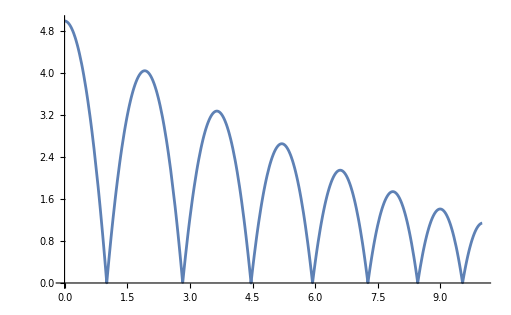

```mathematica
NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]==0,y'[t]->-0.9y'[t]]},y,{t,0,10}]
ynum=(y/.Flatten@%)[t];
Plot[ynum,{t,0,10}]
```

Much like “DSolve”, “NDSolve” is very versatile and can even solve PDEs numerically. The downside is that it has the same pitfalls as other numerical methods in Mathematica, i.e. they can be painfully slow.

## Exercises

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

Q4: Find the series expansion of the function f(x) = e^(-arctan(x)) about x=0, and about x → ∞. Hint: The arctan function is ArcTan[x].

Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

Q1:

```mathematica
f[x_]:=x Exp[-x]+x(1-x)
```

```mathematica
f[{0, 0.1, 0.2, 0.4, 0.8}]
```

{0,0.180484,0.323746,0.508128,0.519463}

Q2:

{x1→3.83171}

{x2→7.01559}

{x3→10.1735}

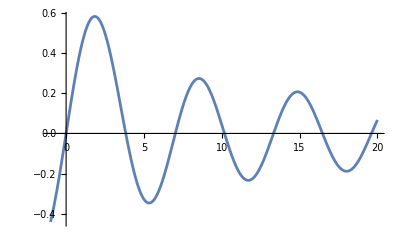

```mathematica
FindRoot[BesselJ[1,x1]==0,{x1,4}]
FindRoot[BesselJ[1,x2]==0,{x2, 7}]
FindRoot[BesselJ[1,x3]==0,{x3,10}]
Plot[BesselJ[1,x],{x,-1,20}]
```

Q3

```mathematica
Simplify[D[Integrate[Sin[x]Exp[-x],x],x]]
```

ⅇ^-x Sin[x]

Q4

```mathematica
Series[Exp[-ArcTan[x]],{x, 0, 5}]
```

1-x+x^2/2+x^3/6-(7 x^4)/24-x^5/24+O[x]^6

```mathematica
Series[Exp[-ArcTan[x]],{x, ∞, 5}]
```

ⅇ^(-π/2)+ⅇ^(-π/2)/x+ⅇ^(-π/2)/(2 x^2)-ⅇ^(-π/2)/(6 x^3)-(7 ⅇ^(-π/2))/(24 x^4)+ⅇ^(-π/2)/(24 x^5)+O[1/x]^6

Q5

```mathematica
Clear[x]
DSolve[{y''[x]-x y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y[x],x]
```

{{y[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

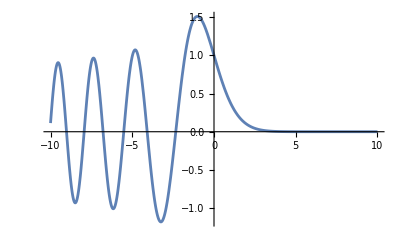

```mathematica
Plot[3^(2/3) AiryAi[x] Gamma[2/3], {x,-10,10}]
```

```mathematica
Clear[x]
sol=NDSolve[{y''[x]-x y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y,{x,-10,10},Method->"ImplicitRungeKutta",AccuracyGoal->13,PrecisionGoal->13,MaxSteps->Infinity]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Clear[ynum]
ynum=(y/.Flatten@sol)[x];
```

```mathematica
ynum[[0]]
PropertyList[%]
```

InterpolatingFunction[…]

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid,VectorEvaluate}

```mathematica
ynum[[0]]["ValuesOnGrid"]
Flatten@ynum[[0]]["Coordinates"]
ydat=Transpose[{%,%%}]
```

{0.113347,0.148928,0.184268,0.229345,0.27381,0.314086,0.352949,0.391044,0.427049,0.463545,0.496416,0.526622,0.555955,0.584365,0.611807,0.638238,0.660331,0.678474,0.696008,0.711964,0.727352,0.742162,0.757721,0.772027,0.785649,0.798226,0.810137,0.821371,0.831921,0.841777,0.851121,0.859727,0.86729,0.87416,0.880241,0.885642,0.890359,0.89439,0.897732,0.900706,0.902776,0.903903,0.904216,0.903953,0.902954,0.901363,0.899135,0.895473,0.890831,0.882784,0.873084,0.861623,0.848424,0.828136,0.80488,0.779332,0.752617,0.724906,0.695162,0.658158,0.618671,0.576855,0.532872,0.486892,0.439091,0.389652,0.338761,0.294909,0.251754,0.209094,0.165947,0.122413,0.0785954,0.0356865,-0.00730098,-0.0468644,-0.0850705,-0.123129,-0.166059,-0.214533,-0.262386,-0.309481,-0.355685,-0.400865,-0.444894,-0.483268,-0.520531,-0.554279,-0.586395,-0.616185,-0.644143,-0.671016,-0.693375,-0.714758,-0.733817,-0.752089,-0.768739,-0.784644,-0.799686,-0.813965,-0.827468,-0.841995,-0.855467,-0.869645,-0.882385,-0.891186,-0.899063,-0.90608,-0.911892,-0.916933,-0.9212,-0.924689,-0.9274,-0.929453,-0.930592,-0.930781,-0.929877,-0.927909,-0.924384,-0.919496,-0.912189,-0.903104,-0.892261,-0.879685,-0.863171,-0.844461,-0.823718,-0.800909,-0.772187,-0.740914,-0.707198,-0.671156,-0.63392,-0.594713,-0.553971,-0.511943,-0.467727,-0.422762,-0.380163,-0.336605,-0.292994,-0.2494,-0.205222,-0.160566,-0.115535,-0.0702353,-0.0247729,0.0207469,0.0662188,0.111538,0.156601,0.198498,0.239997,0.281014,0.328097,0.374289,0.414309,0.453453,0.491641,0.523103,0.55378,0.583429,0.612218,0.640106,0.667055,0.693026,0.717983,0.741892,0.764719,0.786433,0.805444,0.823463,0.840467,0.856439,0.873614,0.889356,0.903641,0.915985,0.925749,0.934423,0.941999,0.948495,0.952969,0.956695,0.959668,0.96189,0.963359,0.964118,0.963882,0.962365,0.958957,0.95274,0.944754,0.934698,0.919354,0.897983,0.867587,0.830516,0.79374,0.756989,0.717158,0.674422,0.624729,0.572047,0.525812,0.477824,0.428248,0.377253,0.325012,0.271701,0.217498,0.166953,0.115947,0.0646205,0.0192771,-0.0261073,-0.0714364,-0.119628,-0.167532,-0.212115,-0.253616,-0.292398,-0.330698,-0.369899,-0.405699,-0.440881,-0.475394,-0.509187,-0.54221,-0.574966,-0.606827,-0.635852,-0.663953,-0.691154,-0.71742,-0.741341,-0.764299,-0.786346,-0.806942,-0.826467,-0.845078,-0.862756,-0.879484,-0.894777,-0.909147,-0.921292,-0.932254,-0.942498,-0.952017,-0.960185,-0.967705,-0.974185,-0.979826,-0.984958,-0.989581,-0.993692,-0.997289,-1.00037,-1.00314,-1.0053,-1.00685,-1.00786,-1.0081,-1.00743,-1.00579,-1.00318,-0.998996,-0.992566,-0.982404,-0.967457,-0.949209,-0.927735,-0.903122,-0.87114,-0.835312,-0.798357,-0.762096,-0.723419,-0.676859,-0.627568,-0.575758,-0.523535,-0.469369,-0.413468,-0.352722,-0.30117,-0.248772,-0.2018,-0.154386,-0.106636,-0.0518057,0.00317125,0.0448976,0.0865515,0.128066,0.17505,0.221671,0.274246,0.321858,0.36875,0.414819,0.462008,0.507024,0.550874,0.589667,0.627346,0.660618,0.692864,0.727171,0.760114,0.791637,0.820348,0.843664,0.86441,0.884249,0.903165,0.923412,0.942434,0.960209,0.976718,0.991943,1.0077,1.02174,1.03407,1.04348,1.05154,1.05824,1.0641,1.06754,1.06976,1.07108,1.07146,1.07065,1.06864,1.06451,1.05895,1.05179,1.04306,1.03395,1.02363,1.01022,0.995868,0.980092,0.962916,0.94437,0.9219,0.897782,0.874025,0.84894,0.822978,0.795813,0.766653,0.737097,0.70647,0.674821,0.642199,0.615287,0.588423,0.561644,0.534393,0.506695,0.478572,0.450051,0.421157,0.391913,0.362347,0.332482,0.302345,0.273692,0.231408,0.189225,0.120866,0.0520412,-0.0285555,-0.109005,-0.188896,-0.264565,-0.339009,-0.418504,-0.495731,-0.574479,-0.649816,-0.721335,-0.776562,-0.828766,-0.875637,-0.919511,-0.960392,-0.998003,-1.03015,-1.0593,-1.08507,-1.1078,-1.12748,-1.14143,-1.15324,-1.16327,-1.17097,-1.17773,-1.18011,-1.17951,-1.17608,-1.16988,-1.16228,-1.15265,-1.14198,-1.12963,-1.11321,-1.09462,-1.06923,-1.04082,-1.0095,-0.975398,-0.940474,-0.903244,-0.863823,-0.812036,-0.755087,-0.695201,-0.634209,-0.572035,-0.507899,-0.442043,-0.374711,-0.306147,-0.232449,-0.163345,-0.0937438,-0.0260591,0.0416981,0.109342,0.176693,0.249111,0.320769,0.39013,0.460136,0.528791,0.595921,0.661363,0.720142,0.777245,0.832094,0.881159,0.928591,0.981794,1.03261,1.08097,1.12682,1.17009,1.21076,1.24786,1.28446,1.32163,1.35487,1.38473,1.41465,1.44025,1.45856,1.4739,1.48773,1.49923,1.5059,1.50867,1.50771,1.50321,1.49337,1.47902,1.46049,1.44103,1.41886,1.39072,1.35974,1.32803,1.29594,1.2667,1.23644,1.20705,1.1801,1.15463,1.13296,1.11109,1.09456,1.07868,1.06511,1.0535,1.04401,1.03622,1.02894,1.02322,1.0175,1.01338,1.0094,1.00705,1.00499,1.00356,1.00249,1.00166,1.00107,1.00066,1.0004,1.00022,1.00013,1.00007,1.00004,1.00002,1.00001,1.,1.,1.,1.,1.,1.,0.999999,0.999997,0.999995,0.99999,0.999981,0.999965,0.999926,0.999872,0.999778,0.999578,0.999323,0.998927,0.998362,0.997641,0.996618,0.995595,0.994135,0.992161,0.990187,0.987473,0.984759,0.98133,0.975918,0.970507,0.963061,0.955619,0.941842,0.930395,0.915539,0.900727,0.885968,0.86719,0.850438,0.833783,0.813425,0.793245,0.773257,0.753474,0.733911,0.71458,0.695491,0.676655,0.656691,0.637042,0.617717,0.596922,0.576537,0.556573,0.537035,0.517931,0.499267,0.479727,0.460701,0.442192,0.424199,0.406724,0.386217,0.370388,0.355038,0.341104,0.327582,0.314467,0.300217,0.286467,0.273209,0.260434,0.248377,0.237778,0.227543,0.217383,0.207592,0.19898,0.190661,0.182629,0.174878,0.167402,0.160193,0.153244,0.146551,0.140104,0.133899,0.127929,0.120942,0.114284,0.1076,0.101256,0.0952373,0.0895314,0.0841254,0.0778396,0.0725252,0.066438,0.0608065,0.054997,0.0496869,0.0448397,0.0404209,0.0363979,0.03274,0.0294183,0.0261998,0.0233054,0.0200733,0.0172571,0.0148084,0.0126839,0.0106179,0.00886799,0.0074146,0.00618595,0.00512678,0.0042395,0.00348262,0.00285433,0.00233148,0.0019001,0.00153115,0.00123087,0.000982044,0.000781586,0.000620524,0.000484749,0.000377665,0.000293454,0.00022742,0.000175785,0.000135523,0.000098499,0.0000691031,0.0000482653,0.0000336455,0.0000233487,0.0000161381,0.0000110959,7.57818×10^-6,5.13179×10^-6,3.44023×10^-6,2.27977×10^-6,1.49135×10^-6,9.61639×10^-7,6.1023×10^-7,3.80438×10^-7,2.32591×10^-7,1.39196×10^-7,8.14191×10^-8,4.65576×10^-8,2.6211×10^-8,1.49992×10^-8,9.71203×10^-9,8.8321×10^-9,1.23134×10^-8,2.06802×10^-8,3.42141×10^-8,4.44578×10^-8,5.79954×10^-8}

{-10.,-9.98728,-9.97457,-9.95819,-9.94181,-9.92674,-9.91194,-9.89713,-9.88283,-9.86797,-9.85422,-9.84123,-9.82824,-9.81525,-9.80226,-9.78927,-9.77799,-9.7684,-9.75881,-9.74977,-9.74073,-9.73169,-9.72177,-9.71222,-9.70267,-9.69339,-9.6841,-9.67482,-9.66553,-9.65625,-9.64676,-9.63728,-9.62817,-9.61906,-9.61009,-9.60113,-9.59216,-9.5832,-9.57423,-9.56398,-9.55373,-9.54398,-9.5358,-9.52762,-9.51833,-9.5097,-9.50108,-9.49034,-9.4796,-9.46471,-9.4501,-9.43548,-9.42087,-9.40134,-9.38182,-9.36271,-9.34457,-9.32723,-9.30988,-9.28973,-9.26957,-9.24942,-9.22926,-9.20911,-9.18895,-9.1688,-9.14864,-9.13166,-9.11524,-9.09924,-9.08323,-9.06723,-9.05122,-9.03561,-9.02,-9.00563,-8.99172,-8.97781,-8.96203,-8.94404,-8.92605,-8.90806,-8.89007,-8.87208,-8.85409,-8.83797,-8.82185,-8.80679,-8.79197,-8.77773,-8.76387,-8.75,-8.738,-8.72605,-8.71496,-8.70386,-8.6933,-8.68274,-8.67225,-8.66176,-8.65127,-8.63923,-8.62719,-8.61334,-8.59948,-8.58884,-8.57828,-8.56772,-8.55777,-8.54783,-8.53789,-8.52795,-8.51801,-8.50726,-8.4965,-8.48445,-8.47283,-8.4612,-8.44799,-8.43478,-8.41956,-8.40434,-8.38912,-8.37391,-8.35646,-8.33901,-8.32165,-8.30429,-8.28432,-8.26434,-8.24437,-8.22439,-8.20493,-8.18546,-8.16614,-8.147,-8.12758,-8.10844,-8.09078,-8.07313,-8.05578,-8.03872,-8.02166,-8.0046,-7.98754,-7.97048,-7.95342,-7.93636,-7.9193,-7.90224,-7.88518,-7.86919,-7.8532,-7.83722,-7.81859,-7.79996,-7.78349,-7.76701,-7.75053,-7.73661,-7.72269,-7.70886,-7.69504,-7.68121,-7.66738,-7.65355,-7.63973,-7.6259,-7.61207,-7.59825,-7.5855,-7.57275,-7.56,-7.54725,-7.53249,-7.51773,-7.50297,-7.48878,-7.47623,-7.46369,-7.45114,-7.43854,-7.42826,-7.41797,-7.40769,-7.3974,-7.38712,-7.37529,-7.36345,-7.34973,-7.33389,-7.31538,-7.29805,-7.28072,-7.25918,-7.23451,-7.20531,-7.17508,-7.14872,-7.12483,-7.10094,-7.07704,-7.05099,-7.02494,-7.00312,-6.9813,-6.95948,-6.93766,-6.91583,-6.89401,-6.87219,-6.8521,-6.83201,-6.81191,-6.79422,-6.77653,-6.75884,-6.73997,-6.72109,-6.70338,-6.68674,-6.67101,-6.65528,-6.63895,-6.62379,-6.60863,-6.59346,-6.5783,-6.56314,-6.54772,-6.53229,-6.51783,-6.50339,-6.48896,-6.47452,-6.46089,-6.44729,-6.4337,-6.42045,-6.40731,-6.39418,-6.38104,-6.3679,-6.35516,-6.34242,-6.33095,-6.31991,-6.30887,-6.29783,-6.28759,-6.27739,-6.26781,-6.25871,-6.2496,-6.2405,-6.23139,-6.22229,-6.21318,-6.20327,-6.19335,-6.18344,-6.17222,-6.16101,-6.14848,-6.13595,-6.12342,-6.10902,-6.09234,-6.07192,-6.04817,-6.02441,-6.00066,-5.9769,-5.94965,-5.9224,-5.89684,-5.8736,-5.85037,-5.82405,-5.79773,-5.77141,-5.74599,-5.72057,-5.69515,-5.66828,-5.64597,-5.62366,-5.6039,-5.58415,-5.56439,-5.54183,-5.51926,-5.50213,-5.485,-5.46788,-5.44839,-5.4289,-5.40669,-5.3863,-5.36591,-5.34553,-5.32421,-5.30339,-5.28256,-5.26362,-5.24468,-5.22744,-5.2102,-5.19119,-5.17218,-5.15317,-5.13503,-5.11961,-5.10529,-5.09096,-5.07663,-5.06043,-5.04424,-5.02804,-5.01185,-4.99565,-4.97721,-4.95877,-4.94033,-4.92409,-4.90785,-4.89161,-4.87349,-4.85916,-4.84589,-4.83263,-4.81737,-4.80211,-4.78685,-4.768,-4.75019,-4.73238,-4.71457,-4.69868,-4.6828,-4.66449,-4.64692,-4.62936,-4.61179,-4.59422,-4.57446,-4.55469,-4.53638,-4.51808,-4.50005,-4.48203,-4.46348,-4.4454,-4.42732,-4.40924,-4.39116,-4.37662,-4.3624,-4.34849,-4.33458,-4.32067,-4.30677,-4.29286,-4.27895,-4.26504,-4.25113,-4.23723,-4.22332,-4.2102,-4.191,-4.17201,-4.14149,-4.11096,-4.07532,-4.03969,-4.00405,-3.96989,-3.93574,-3.89845,-3.86115,-3.82173,-3.7823,-3.74288,-3.71073,-3.67861,-3.64797,-3.61734,-3.5866,-3.55587,-3.52714,-3.4984,-3.47004,-3.44169,-3.41333,-3.38985,-3.36637,-3.34194,-3.31752,-3.28429,-3.25615,-3.22883,-3.20152,-3.17439,-3.15082,-3.12726,-3.1055,-3.08374,-3.05846,-3.03319,-3.00253,-2.97187,-2.94121,-2.91055,-2.88138,-2.85222,-2.82305,-2.78686,-2.74925,-2.71164,-2.67495,-2.63889,-2.60283,-2.56677,-2.53071,-2.49465,-2.45646,-2.42104,-2.38561,-2.3513,-2.31699,-2.28268,-2.24837,-2.21121,-2.17404,-2.13759,-2.10019,-2.06279,-2.02539,-1.98799,-1.95346,-1.91894,-1.88472,-1.85309,-1.82146,-1.78456,-1.74765,-1.71074,-1.67384,-1.63693,-1.60003,-1.56405,-1.52589,-1.48366,-1.442,-1.40035,-1.35288,-1.30542,-1.26539,-1.22535,-1.18026,-1.12834,-1.07937,-1.03041,-0.98144,-0.932473,-0.87363,-0.814787,-0.755945,-0.704219,-0.652493,-0.593811,-0.535129,-0.479464,-0.426368,-0.380114,-0.333859,-0.290184,-0.250993,-0.214539,-0.183894,-0.153249,-0.130243,-0.108231,-0.0894755,-0.0734767,-0.0604224,-0.0497111,-0.0397077,-0.031861,-0.0240143,-0.0183566,-0.0128981,-0.00966436,-0.00684991,-0.00488492,-0.00340947,-0.00227404,-0.0014651,-0.000912158,-0.000547425,-0.00030193,-0.000174629,-0.0000953594,-0.0000531255,-0.00002767,-0.0000148076,-6.65355×10^-6,-3.18573×10^-6,-1.19417×10^-6,-5.97083×10^-7,0.,5.97084×10^-7,1.19417×10^-6,3.54667×10^-6,6.75903×10^-6,0.0000143427,0.0000264329,0.0000485806,0.000101146,0.000175857,0.000304557,0.000578281,0.000929158,0.00147196,0.00224738,0.00323612,0.00463964,0.00604316,0.00804473,0.0107529,0.0134612,0.0171846,0.0209081,0.0256142,0.0330426,0.040471,0.0506996,0.0609283,0.0798894,0.0956719,0.116201,0.13673,0.157259,0.183496,0.207034,0.230572,0.25955,0.288528,0.317507,0.346485,0.375464,0.404442,0.43342,0.462399,0.493564,0.524729,0.555893,0.590048,0.624203,0.658358,0.692512,0.726667,0.760822,0.79748,0.834138,0.870796,0.907455,0.944113,0.988585,1.02409,1.05959,1.09281,1.12602,1.15924,1.19654,1.23385,1.27115,1.30846,1.34501,1.37832,1.41163,1.4459,1.48018,1.51143,1.54268,1.57394,1.60519,1.63644,1.6677,1.69895,1.7302,1.76146,1.79271,1.82396,1.86215,1.90034,1.94064,1.98094,2.02124,2.06155,2.10185,2.15166,2.1966,2.25178,2.30697,2.36887,2.43077,2.49267,2.55457,2.61647,2.67837,2.74027,2.80663,2.87299,2.95665,3.0403,3.12396,3.20762,3.30247,3.39733,3.49043,3.58354,3.67891,3.77428,3.87182,3.96937,4.06747,4.16556,4.26792,4.37028,4.47502,4.57976,4.6845,4.79537,4.90625,5.01713,5.12801,5.23889,5.34977,5.48432,5.63197,5.77962,5.92628,6.07304,6.21971,6.36679,6.51485,6.66457,6.81651,6.97115,7.12895,7.29035,7.45585,7.62596,7.80122,7.98222,8.16964,8.36418,8.56662,8.77765,8.99748,9.22431,9.45108,9.65533,9.82766,9.91383,10.}

{{-10.,0.113347},{-9.98728,0.148928},{-9.97457,0.184268},{-9.95819,0.229345},{-9.94181,0.27381},{-9.92674,0.314086},{-9.91194,0.352949},{-9.89713,0.391044},{-9.88283,0.427049},{-9.86797,0.463545},{-9.85422,0.496416},{-9.84123,0.526622},{-9.82824,0.555955},{-9.81525,0.584365},{-9.80226,0.611807},{-9.78927,0.638238},{-9.77799,0.660331},{-9.7684,0.678474},{-9.75881,0.696008},{-9.74977,0.711964},{-9.74073,0.727352},{-9.73169,0.742162},{-9.72177,0.757721},{-9.71222,0.772027},{-9.70267,0.785649},{-9.69339,0.798226},{-9.6841,0.810137},{-9.67482,0.821371},{-9.66553,0.831921},{-9.65625,0.841777},{-9.64676,0.851121},{-9.63728,0.859727},{-9.62817,0.86729},{-9.61906,0.87416},{-9.61009,0.880241},{-9.60113,0.885642},{-9.59216,0.890359},{-9.5832,0.89439},{-9.57423,0.897732},{-9.56398,0.900706},{-9.55373,0.902776},{-9.54398,0.903903},{-9.5358,0.904216},{-9.52762,0.903953},{-9.51833,0.902954},{-9.5097,0.901363},{-9.50108,0.899135},{-9.49034,0.895473},{-9.4796,0.890831},{-9.46471,0.882784},{-9.4501,0.873084},{-9.43548,0.861623},{-9.42087,0.848424},{-9.40134,0.828136},{-9.38182,0.80488},{-9.36271,0.779332},{-9.34457,0.752617},{-9.32723,0.724906},{-9.30988,0.695162},{-9.28973,0.658158},{-9.26957,0.618671},{-9.24942,0.576855},{-9.22926,0.532872},{-9.20911,0.486892},{-9.18895,0.439091},{-9.1688,0.389652},{-9.14864,0.338761},{-9.13166,0.294909},{-9.11524,0.251754},{-9.09924,0.209094},{-9.08323,0.165947},{-9.06723,0.122413},{-9.05122,0.0785954},{-9.03561,0.0356865},{-9.02,-0.00730098},{-9.00563,-0.0468644},{-8.99172,-0.0850705},{-8.97781,-0.123129},{-8.96203,-0.166059},{-8.94404,-0.214533},{-8.92605,-0.262386},{-8.90806,-0.309481},{-8.89007,-0.355685},{-8.87208,-0.400865},{-8.85409,-0.444894},{-8.83797,-0.483268},{-8.82185,-0.520531},{-8.80679,-0.554279},{-8.79197,-0.586395},{-8.77773,-0.616185},{-8.76387,-0.644143},{-8.75,-0.671016},{-8.738,-0.693375},{-8.72605,-0.714758},{-8.71496,-0.733817},{-8.70386,-0.752089},{-8.6933,-0.768739},{-8.68274,-0.784644},{-8.67225,-0.799686},{-8.66176,-0.813965},{-8.65127,-0.827468},{-8.63923,-0.841995},{-8.62719,-0.855467},{-8.61334,-0.869645},{-8.59948,-0.882385},{-8.58884,-0.891186},{-8.57828,-0.899063},{-8.56772,-0.90608},{-8.55777,-0.911892},{-8.54783,-0.916933},{-8.53789,-0.9212},{-8.52795,-0.924689},{-8.51801,-0.9274},{-8.50726,-0.929453},{-8.4965,-0.930592},{-8.48445,-0.930781},{-8.47283,-0.929877},{-8.4612,-0.927909},{-8.44799,-0.924384},{-8.43478,-0.919496},{-8.41956,-0.912189},{-8.40434,-0.903104},{-8.38912,-0.892261},{-8.37391,-0.879685},{-8.35646,-0.863171},{-8.33901,-0.844461},{-8.32165,-0.823718},{-8.30429,-0.800909},{-8.28432,-0.772187},{-8.26434,-0.740914},{-8.24437,-0.707198},{-8.22439,-0.671156},{-8.20493,-0.63392},{-8.18546,-0.594713},{-8.16614,-0.553971},{-8.147,-0.511943},{-8.12758,-0.467727},{-8.10844,-0.422762},{-8.09078,-0.380163},{-8.07313,-0.336605},{-8.05578,-0.292994},{-8.03872,-0.2494},{-8.02166,-0.205222},{-8.0046,-0.160566},{-7.98754,-0.115535},{-7.97048,-0.0702353},{-7.95342,-0.0247729},{-7.93636,0.0207469},{-7.9193,0.0662188},{-7.90224,0.111538},{-7.88518,0.156601},{-7.86919,0.198498},{-7.8532,0.239997},{-7.83722,0.281014},{-7.81859,0.328097},{-7.79996,0.374289},{-7.78349,0.414309},{-7.76701,0.453453},{-7.75053,0.491641},{-7.73661,0.523103},{-7.72269,0.55378},{-7.70886,0.583429},{-7.69504,0.612218},{-7.68121,0.640106},{-7.66738,0.667055},{-7.65355,0.693026},{-7.63973,0.717983},{-7.6259,0.741892},{-7.61207,0.764719},{-7.59825,0.786433},{-7.5855,0.805444},{-7.57275,0.823463},{-7.56,0.840467},{-7.54725,0.856439},{-7.53249,0.873614},{-7.51773,0.889356},{-7.50297,0.903641},{-7.48878,0.915985},{-7.47623,0.925749},{-7.46369,0.934423},{-7.45114,0.941999},{-7.43854,0.948495},{-7.42826,0.952969},{-7.41797,0.956695},{-7.40769,0.959668},{-7.3974,0.96189},{-7.38712,0.963359},{-7.37529,0.964118},{-7.36345,0.963882},{-7.34973,0.962365},{-7.33389,0.958957},{-7.31538,0.95274},{-7.29805,0.944754},{-7.28072,0.934698},{-7.25918,0.919354},{-7.23451,0.897983},{-7.20531,0.867587},{-7.17508,0.830516},{-7.14872,0.79374},{-7.12483,0.756989},{-7.10094,0.717158},{-7.07704,0.674422},{-7.05099,0.624729},{-7.02494,0.572047},{-7.00312,0.525812},{-6.9813,0.477824},{-6.95948,0.428248},{-6.93766,0.377253},{-6.91583,0.325012},{-6.89401,0.271701},{-6.87219,0.217498},{-6.8521,0.166953},{-6.83201,0.115947},{-6.81191,0.0646205},{-6.79422,0.0192771},{-6.77653,-0.0261073},{-6.75884,-0.0714364},{-6.73997,-0.119628},{-6.72109,-0.167532},{-6.70338,-0.212115},{-6.68674,-0.253616},{-6.67101,-0.292398},{-6.65528,-0.330698},{-6.63895,-0.369899},{-6.62379,-0.405699},{-6.60863,-0.440881},{-6.59346,-0.475394},{-6.5783,-0.509187},{-6.56314,-0.54221},{-6.54772,-0.574966},{-6.53229,-0.606827},{-6.51783,-0.635852},{-6.50339,-0.663953},{-6.48896,-0.691154},{-6.47452,-0.71742},{-6.46089,-0.741341},{-6.44729,-0.764299},{-6.4337,-0.786346},{-6.42045,-0.806942},{-6.40731,-0.826467},{-6.39418,-0.845078},{-6.38104,-0.862756},{-6.3679,-0.879484},{-6.35516,-0.894777},{-6.34242,-0.909147},{-6.33095,-0.921292},{-6.31991,-0.932254},{-6.30887,-0.942498},{-6.29783,-0.952017},{-6.28759,-0.960185},{-6.27739,-0.967705},{-6.26781,-0.974185},{-6.25871,-0.979826},{-6.2496,-0.984958},{-6.2405,-0.989581},{-6.23139,-0.993692},{-6.22229,-0.997289},{-6.21318,-1.00037},{-6.20327,-1.00314},{-6.19335,-1.0053},{-6.18344,-1.00685},{-6.17222,-1.00786},{-6.16101,-1.0081},{-6.14848,-1.00743},{-6.13595,-1.00579},{-6.12342,-1.00318},{-6.10902,-0.998996},{-6.09234,-0.992566},{-6.07192,-0.982404},{-6.04817,-0.967457},{-6.02441,-0.949209},{-6.00066,-0.927735},{-5.9769,-0.903122},{-5.94965,-0.87114},{-5.9224,-0.835312},{-5.89684,-0.798357},{-5.8736,-0.762096},{-5.85037,-0.723419},{-5.82405,-0.676859},{-5.79773,-0.627568},{-5.77141,-0.575758},{-5.74599,-0.523535},{-5.72057,-0.469369},{-5.69515,-0.413468},{-5.66828,-0.352722},{-5.64597,-0.30117},{-5.62366,-0.248772},{-5.6039,-0.2018},{-5.58415,-0.154386},{-5.56439,-0.106636},{-5.54183,-0.0518057},{-5.51926,0.00317125},{-5.50213,0.0448976},{-5.485,0.0865515},{-5.46788,0.128066},{-5.44839,0.17505},{-5.4289,0.221671},{-5.40669,0.274246},{-5.3863,0.321858},{-5.36591,0.36875},{-5.34553,0.414819},{-5.32421,0.462008},{-5.30339,0.507024},{-5.28256,0.550874},{-5.26362,0.589667},{-5.24468,0.627346},{-5.22744,0.660618},{-5.2102,0.692864},{-5.19119,0.727171},{-5.17218,0.760114},{-5.15317,0.791637},{-5.13503,0.820348},{-5.11961,0.843664},{-5.10529,0.86441},{-5.09096,0.884249},{-5.07663,0.903165},{-5.06043,0.923412},{-5.04424,0.942434},{-5.02804,0.960209},{-5.01185,0.976718},{-4.99565,0.991943},{-4.97721,1.0077},{-4.95877,1.02174},{-4.94033,1.03407},{-4.92409,1.04348},{-4.90785,1.05154},{-4.89161,1.05824},{-4.87349,1.0641},{-4.85916,1.06754},{-4.84589,1.06976},{-4.83263,1.07108},{-4.81737,1.07146},{-4.80211,1.07065},{-4.78685,1.06864},{-4.768,1.06451},{-4.75019,1.05895},{-4.73238,1.05179},{-4.71457,1.04306},{-4.69868,1.03395},{-4.6828,1.02363},{-4.66449,1.01022},{-4.64692,0.995868},{-4.62936,0.980092},{-4.61179,0.962916},{-4.59422,0.94437},{-4.57446,0.9219},{-4.55469,0.897782},{-4.53638,0.874025},{-4.51808,0.84894},{-4.50005,0.822978},{-4.48203,0.795813},{-4.46348,0.766653},{-4.4454,0.737097},{-4.42732,0.70647},{-4.40924,0.674821},{-4.39116,0.642199},{-4.37662,0.615287},{-4.3624,0.588423},{-4.34849,0.561644},{-4.33458,0.534393},{-4.32067,0.506695},{-4.30677,0.478572},{-4.29286,0.450051},{-4.27895,0.421157},{-4.26504,0.391913},{-4.25113,0.362347},{-4.23723,0.332482},{-4.22332,0.302345},{-4.2102,0.273692},{-4.191,0.231408},{-4.17201,0.189225},{-4.14149,0.120866},{-4.11096,0.0520412},{-4.07532,-0.0285555},{-4.03969,-0.109005},{-4.00405,-0.188896},{-3.96989,-0.264565},{-3.93574,-0.339009},{-3.89845,-0.418504},{-3.86115,-0.495731},{-3.82173,-0.574479},{-3.7823,-0.649816},{-3.74288,-0.721335},{-3.71073,-0.776562},{-3.67861,-0.828766},{-3.64797,-0.875637},{-3.61734,-0.919511},{-3.5866,-0.960392},{-3.55587,-0.998003},{-3.52714,-1.03015},{-3.4984,-1.0593},{-3.47004,-1.08507},{-3.44169,-1.1078},{-3.41333,-1.12748},{-3.38985,-1.14143},{-3.36637,-1.15324},{-3.34194,-1.16327},{-3.31752,-1.17097},{-3.28429,-1.17773},{-3.25615,-1.18011},{-3.22883,-1.17951},{-3.20152,-1.17608},{-3.17439,-1.16988},{-3.15082,-1.16228},{-3.12726,-1.15265},{-3.1055,-1.14198},{-3.08374,-1.12963},{-3.05846,-1.11321},{-3.03319,-1.09462},{-3.00253,-1.06923},{-2.97187,-1.04082},{-2.94121,-1.0095},{-2.91055,-0.975398},{-2.88138,-0.940474},{-2.85222,-0.903244},{-2.82305,-0.863823},{-2.78686,-0.812036},{-2.74925,-0.755087},{-2.71164,-0.695201},{-2.67495,-0.634209},{-2.63889,-0.572035},{-2.60283,-0.507899},{-2.56677,-0.442043},{-2.53071,-0.374711},{-2.49465,-0.306147},{-2.45646,-0.232449},{-2.42104,-0.163345},{-2.38561,-0.0937438},{-2.3513,-0.0260591},{-2.31699,0.0416981},{-2.28268,0.109342},{-2.24837,0.176693},{-2.21121,0.249111},{-2.17404,0.320769},{-2.13759,0.39013},{-2.10019,0.460136},{-2.06279,0.528791},{-2.02539,0.595921},{-1.98799,0.661363},{-1.95346,0.720142},{-1.91894,0.777245},{-1.88472,0.832094},{-1.85309,0.881159},{-1.82146,0.928591},{-1.78456,0.981794},{-1.74765,1.03261},{-1.71074,1.08097},{-1.67384,1.12682},{-1.63693,1.17009},{-1.60003,1.21076},{-1.56405,1.24786},{-1.52589,1.28446},{-1.48366,1.32163},{-1.442,1.35487},{-1.40035,1.38473},{-1.35288,1.41465},{-1.30542,1.44025},{-1.26539,1.45856},{-1.22535,1.4739},{-1.18026,1.48773},{-1.12834,1.49923},{-1.07937,1.5059},{-1.03041,1.50867},{-0.98144,1.50771},{-0.932473,1.50321},{-0.87363,1.49337},{-0.814787,1.47902},{-0.755945,1.46049},{-0.704219,1.44103},{-0.652493,1.41886},{-0.593811,1.39072},{-0.535129,1.35974},{-0.479464,1.32803},{-0.426368,1.29594},{-0.380114,1.2667},{-0.333859,1.23644},{-0.290184,1.20705},{-0.250993,1.1801},{-0.214539,1.15463},{-0.183894,1.13296},{-0.153249,1.11109},{-0.130243,1.09456},{-0.108231,1.07868},{-0.0894755,1.06511},{-0.0734767,1.0535},{-0.0604224,1.04401},{-0.0497111,1.03622},{-0.0397077,1.02894},{-0.031861,1.02322},{-0.0240143,1.0175},{-0.0183566,1.01338},{-0.0128981,1.0094},{-0.00966436,1.00705},{-0.00684991,1.00499},{-0.00488492,1.00356},{-0.00340947,1.00249},{-0.00227404,1.00166},{-0.0014651,1.00107},{-0.000912158,1.00066},{-0.000547425,1.0004},{-0.00030193,1.00022},{-0.000174629,1.00013},{-0.0000953594,1.00007},{-0.0000531255,1.00004},{-0.00002767,1.00002},{-0.0000148076,1.00001},{-6.65355×10^-6,1.},{-3.18573×10^-6,1.},{-1.19417×10^-6,1.},{-5.97083×10^-7,1.},{0.,1.},{5.97084×10^-7,1.},{1.19417×10^-6,0.999999},{3.54667×10^-6,0.999997},{6.75903×10^-6,0.999995},{0.0000143427,0.99999},{0.0000264329,0.999981},{0.0000485806,0.999965},{0.000101146,0.999926},{0.000175857,0.999872},{0.000304557,0.999778},{0.000578281,0.999578},{0.000929158,0.999323},{0.00147196,0.998927},{0.00224738,0.998362},{0.00323612,0.997641},{0.00463964,0.996618},{0.00604316,0.995595},{0.00804473,0.994135},{0.0107529,0.992161},{0.0134612,0.990187},{0.0171846,0.987473},{0.0209081,0.984759},{0.0256142,0.98133},{0.0330426,0.975918},{0.040471,0.970507},{0.0506996,0.963061},{0.0609283,0.955619},{0.0798894,0.941842},{0.0956719,0.930395},{0.116201,0.915539},{0.13673,0.900727},{0.157259,0.885968},{0.183496,0.86719},{0.207034,0.850438},{0.230572,0.833783},{0.25955,0.813425},{0.288528,0.793245},{0.317507,0.773257},{0.346485,0.753474},{0.375464,0.733911},{0.404442,0.71458},{0.43342,0.695491},{0.462399,0.676655},{0.493564,0.656691},{0.524729,0.637042},{0.555893,0.617717},{0.590048,0.596922},{0.624203,0.576537},{0.658358,0.556573},{0.692512,0.537035},{0.726667,0.517931},{0.760822,0.499267},{0.79748,0.479727},{0.834138,0.460701},{0.870796,0.442192},{0.907455,0.424199},{0.944113,0.406724},{0.988585,0.386217},{1.02409,0.370388},{1.05959,0.355038},{1.09281,0.341104},{1.12602,0.327582},{1.15924,0.314467},{1.19654,0.300217},{1.23385,0.286467},{1.27115,0.273209},{1.30846,0.260434},{1.34501,0.248377},{1.37832,0.237778},{1.41163,0.227543},{1.4459,0.217383},{1.48018,0.207592},{1.51143,0.19898},{1.54268,0.190661},{1.57394,0.182629},{1.60519,0.174878},{1.63644,0.167402},{1.6677,0.160193},{1.69895,0.153244},{1.7302,0.146551},{1.76146,0.140104},{1.79271,0.133899},{1.82396,0.127929},{1.86215,0.120942},{1.90034,0.114284},{1.94064,0.1076},{1.98094,0.101256},{2.02124,0.0952373},{2.06155,0.0895314},{2.10185,0.0841254},{2.15166,0.0778396},{2.1966,0.0725252},{2.25178,0.066438},{2.30697,0.0608065},{2.36887,0.054997},{2.43077,0.0496869},{2.49267,0.0448397},{2.55457,0.0404209},{2.61647,0.0363979},{2.67837,0.03274},{2.74027,0.0294183},{2.80663,0.0261998},{2.87299,0.0233054},{2.95665,0.0200733},{3.0403,0.0172571},{3.12396,0.0148084},{3.20762,0.0126839},{3.30247,0.0106179},{3.39733,0.00886799},{3.49043,0.0074146},{3.58354,0.00618595},{3.67891,0.00512678},{3.77428,0.0042395},{3.87182,0.00348262},{3.96937,0.00285433},{4.06747,0.00233148},{4.16556,0.0019001},{4.26792,0.00153115},{4.37028,0.00123087},{4.47502,0.000982044},{4.57976,0.000781586},{4.6845,0.000620524},{4.79537,0.000484749},{4.90625,0.000377665},{5.01713,0.000293454},{5.12801,0.00022742},{5.23889,0.000175785},{5.34977,0.000135523},{5.48432,0.000098499},{5.63197,0.0000691031},{5.77962,0.0000482653},{5.92628,0.0000336455},{6.07304,0.0000233487},{6.21971,0.0000161381},{6.36679,0.0000110959},{6.51485,7.57818×10^-6},{6.66457,5.13179×10^-6},{6.81651,3.44023×10^-6},{6.97115,2.27977×10^-6},{7.12895,1.49135×10^-6},{7.29035,9.61639×10^-7},{7.45585,6.1023×10^-7},{7.62596,3.80438×10^-7},{7.80122,2.32591×10^-7},{7.98222,1.39196×10^-7},{8.16964,8.14191×10^-8},{8.36418,4.65576×10^-8},{8.56662,2.6211×10^-8},{8.77765,1.49992×10^-8},{8.99748,9.71203×10^-9},{9.22431,8.8321×10^-9},{9.45108,1.23134×10^-8},{9.65533,2.06802×10^-8},{9.82766,3.42141×10^-8},{9.91383,4.44578×10^-8},{10.,5.79954×10^-8}}

```mathematica
Plot[ynum,{x,-10,10}]
```

-Graphics-